Hidden Markov Model analysis of photon traces

```mathematica
Needs["Fretica`"]
```

## Theory

What is a hidden Markov model?, Sean R Eddy , Nature Biotechnologyvolume 22, pages 1315-1316 (2004)https://doi.org/10.1038/nbt1004-1315

#### HHM of a three-state system with two detection channels (donor and acceptor)

-Graphics--Graphics--Graphics-

Note that this is an example model. Fretica is neither limited to three states nor to two detection channels. Arbitrary number of states and detection channels can be processed. The user has the freedom to use any reasonable, custom parameterized rate matrix K. Some rate coefficient can for example  be fixed to  already known values, or ratios of rate coefficiencies  can be constraint to known equilibrium constants. For the 3-state system  above it would  be for example in most cases reasonable to reduce the set of  free parameters by enforcing detailed balance.

#### LogLikelihood for binned photon traces ( time discrete HMM)

Sean A. McKinney, Chirlmin Joo, and Taekjip Ha, Biophys J. 2006 Sep 1; 91(5): 1941-1951https://dx.doi.org/10.1529%2Fbiophysj.106.082487

Yang Liu, Jeehae Park, Karin A. Dahmen, Yann R. Chemla, and Taekjip Ha, J. Phys. Chem. B  	2010 114 (16), 5386-5403 https://doi.org/10.1021/jp9057669

A photon trace is given by a series of time bins (binning Δ) with N_A acceptor and N_D donor photons:
-Graphics-
The logarithm of the likelihoold calculates to 
-Graphics-with  -Graphics-
and -Graphics-

Note that this formalism is assuming that state transitions only occur at the bin boundaries. But not during a bin. Practically, the model is only applicable if the dwell times of the states are much longer than the binning Δ. In this limit one has:

-Graphics-

#### LogLikelihood for photon-by-photon traces ( time continuous HMM)

Irina V. Gopich and Attila Szabo, J. Phys. Chem. B20091133110965-10973https://doi.org/10.1021/jp903671p

Hoi Sung Chung and  Irina V. Gopich, Phys. Chem. Chem. Phys., 2014,16, 18644-18657https://doi.org/10.1039/C4CP02489C

A photon trace is given photon by photon. For each photon the color and the inter-photon time is known.
-Graphics-  -Graphics-
The logarithm of the likelihoold calculates to 
-Graphics-with  -Graphics-
and

#### pini and pfin

pini and pfin are by default set to  pin=peq and pfin=(1,1,..)ᵀ  , where peq is given by K.peq==0 and Total[peq]==1.
However in some cases other choices are desirable.

Hoi Sung Chung, Kevin McHale, John M. Louis, William A. Eaton, Science  2012 Vol. 335, Issue 6071, pp. 981-984https://doi.org/10.1126/science.1215768

#### Multiple time traces

Fretica's HMM machinery can be initialized with a set of multiple binned time traces or with a set of  multiple photon-by-photon time traces. Calling FHMMLogLikelihood will  return the sum over all log-likelihoods of the individual traces. The mean photon rates  of the states can be set and optimized individually  for all  traces. Also pini and pfin can be set individually. The rate matrix K is assumed to be the same for all traces in a set.

#### Viterbi and forward-backward algorithms

Assuming a model consisting of a  rate matrix  and mean photon rates for each state and detection channel one can apply the Viterbi algorithm or the forward-backward algorithm to obtain (most)- probable state trajectories. (The Forward-Backward algorithm is currently only implemented for  binned traces.) Dwell-time distributions of  states can be analyzed. Note, however, that the obtained state trajectories have limited value for estimating the validity of the assumed model.

## Fretica functions

#### Initialisation of the HMM system with binned photon traces or with photon-by-photon traces

```mathematica
?FHMMInitWithBinnedData
```

```mathematica
?FHMMInitWithPhotonByPhotonData
```

```mathematica
?FHMMInitWithPhotonByPhotonDataFromBurstList
```

```mathematica
?FHMMSetPhotonRates
```

```mathematica
?FHMMSetPinPfin
```

#### FHMMLogLikelihood, FHMMGetLogLikelihoodList, FHMMViterbi, and FHMMForwardBackward

```mathematica
?FHMMLogLikelihood
```

```mathematica
?FHMMGetLogLikelihoodList
```

```mathematica
?FHMMViterbi
```

```mathematica
?FHMMForwardBackward
```

#### Photon traces are obtained from measurements (TTTR data) or from simulations

```mathematica
?FHMMGetPhotonByPhotonTraceFromTTTR
```

```mathematica
?FHMMGetBinnedTraceFromTTTR
```

```mathematica
?FHMMSimulatePhotonByPhotonTrace
```

```mathematica
?FHMMBinPhotonByPhotonTrace
```

```mathematica
?FHMMSimulateBinnedTrace
```

#### FHMMViterbi returns an FDwellList

```mathematica
?FDwellList
```

```mathematica
?FRenameStates
```

```mathematica
?FSplitTrajectory
```

## Demonstration for a two-state system

#### Simulation of FRET photon traces

```mathematica
Km[{k12_,k21_}]:=({{-k12, k21}, {k12, -k21}});
```

```mathematica
params={kf->50,ku->100}; (*folding rate and unfolding rate constants*)
K=Km[{kf,ku}/.params];
ntot=50000;
e={0.3,0.8}; (*transfer efficiencies of unfolded and folded state*)

n1=ntot{e,1-e};  (*mean photon rates for first photon trace*)
n2=2ntot{e,1-e}; (*mean photon rates for second photon trace*)

{ptraj1,straj1}=FHMMSimulatePhotonByPhotonTrace[n1,K,3];
{ptraj2,straj2}=FHMMSimulatePhotonByPhotonTrace[n2,K,3];
binning=0.001;
{mcs1,mcs2}={FHMMBinPhotonByPhotonTrace[ptraj1,binning],FHMMBinPhotonByPhotonTrace[ptraj2,binning]};
```

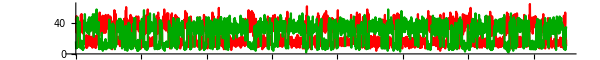

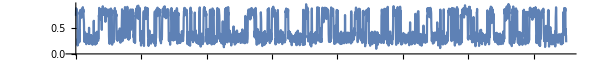

```mathematica
{na,nd}=mcs1ᵀ;
ListPlot[{na,nd},Joined->True,PlotStyle->{Red,Darker@Green},ImageSize->600,AspectRatio->0.1,PlotRange->All]
ListPlot[na/(na+nd),Joined->True,ImageSize->600,AspectRatio->0.1,PlotRange->All]
```

```mathematica
Addt[dat_List]:={binning (Range[Length[dat]]-0.5),dat}ᵀ
```

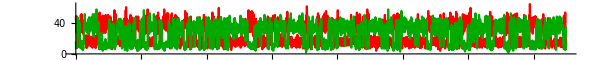

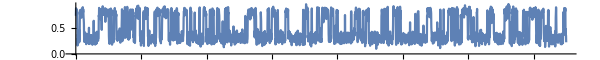

```mathematica
mcspl=ListPlot[{Addt@na,Addt@nd},Joined->True,PlotStyle->{Red,Darker@Green},ImageSize->600,AspectRatio->0.1,PlotRange->All]
ListPlot[Addt@(na/(na+nd)),Joined->True,ImageSize->600,AspectRatio->0.1,PlotRange->All]
```

#### LogLikelihood maximization on binned data

```mathematica
FHMMInitWithBinnedData[{mcs1,mcs2},binning]
```

```mathematica
FHMMSetPhotonRates[{n1,n2}];
FindMaximum[FHMMLogLikelihood[Km[Abs@{kf,ku}]],{{kf,10},{ku,80}},PrecisionGoal->4,AccuracyGoal->4,Method->"IPOPT"]
```

{-40236.1,{kf→52.1675,ku→96.4034}}

```mathematica
FindMaximum[FHMMLogLikelihood[Km[Abs@{kf,ku}],{Abs@nt{e,1-e},Abs@nt2{e,1-e}}],{{kf,10},{ku,80},{nt,40000},{nt2,80000}},PrecisionGoal->4,AccuracyGoal->4,Method->"IPOPT"]
```

{-40234.3,{kf→52.1675,ku→96.4034,nt→50221.3,nt2→100169.}}

#### LogLikelihood maximization on photon-by-photon data

```mathematica
FHMMInitWithPhotonByPhotonData[{ptraj1,ptraj2}]
```

```mathematica
FHMMSetPhotonRates[{n1,n2}];
FindMaximum[FHMMLogLikelihood[Km[Abs@{kf,ku}]],{{kf,60},{ku,80}},PrecisionGoal->4,AccuracyGoal->4,Method->"IPOPT"]
```

{4.37976×10^6,{kf→54.1095,ku→99.3003}}

```mathematica
FindMaximum[FHMMLogLikelihood[Km[Abs@{kf,ku}],{Abs@nt{e,1-e},Abs@nt2{e,1-e}}],{{kf,10},{ku,80},{nt,40000},{nt2,80000}},PrecisionGoal->4,AccuracyGoal->4,Method->"IPOPT"]
```

{4.37976×10^6,{kf→54.1096,ku→99.2994,nt→50222.,nt2→100169.}}

#### Viterbi and dwell-time analysis

```mathematica
FHMMInitWithPhotonByPhotonData[{ptraj1,ptraj2}]
dwells=FHMMViterbi[K,{n1,n2}];
```

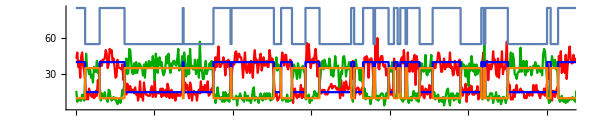

```mathematica
Aratefunc[state_]:=n1[[1,state]]*binning
Dratefunc[state_]:=n1[[2,state]]*binning
viterbimcs={dwells[[1]]["mcs",t0=0,Aratefunc],dwells[[1]]["mcs",0,Dratefunc]};
stategraph=dwells[[1]]["stategraph",t0,scale=30,offset=25];

Show[mcspl
,ListPlot[viterbimcs,PlotRange->All,Joined->True,PlotStyle->{Blue,Orange}]
,ListPlot[stategraph,PlotRange->All,Joined->True]
,PlotRange->{{0,0.5},All},AspectRatio->0.2,ImageSize->600]
```

```mathematica
1/Mean@Flatten@dwells[1->2]["dt"]
1/Mean@Flatten@dwells[2->1]["dt"]
```

51.5696

94.7484

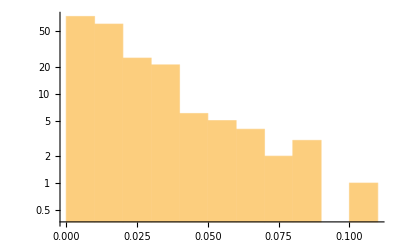

```mathematica
Histogram[Flatten@dwells[1->2]["dt"],Automatic,"LogCount"]
```

```mathematica
dwelltimehisto[trans_]:=Histo[Flatten@dwells[trans]["dt"],{0,0.05,0.01},FOutput->FData][[All,1;;2]]
```

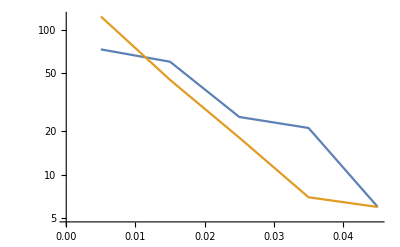

```mathematica
ListLogPlot[{dwelltimehisto[1->2],dwelltimehisto[2->1]},Joined->True]
```

```mathematica
FHMMInitWithPhotonByPhotonData[{FHMMSimulatePhotonByPhotonTrace[n1,K,60][[1]]}]
```

```mathematica
dwells=FHMMViterbi[K,{n1}];
```

```mathematica
dwelltimehisto[trans_]:=Histo[Flatten@dwells[trans]["dt"],{0,0.1,0.01},FOutput->FData][[All,1;;2]]
```

```mathematica
ListLogPlot[{dwelltimehisto[1->2],dwelltimehisto[2->1]},PlotRange->All]
```

-Graphics-

## 3-color FRET

#### Simulation of FRET photon traces

```mathematica
Km[{k12_,k21_,k23_,k32_}]:=({{-k12, k21, 0}, {k12, -k21-k23, k32}, {0, k23, -k32}});
```

```mathematica
params={k12->50,k21->20,k23->10,k32->30}; 
K=Km[{k12,k21,k23,k32}/.params];
ntot=50000;
pBB={0.5,0.3,0.1}; (*probabilites of the three states that an emitted photon is blue after blue excitation *)
pBG={0.4,0.3,0.1}; (*probabilites of the three states that an emitted photon is green after blue excitation *)
pBR={0.1,0.4,0.8}; (*probabilites of the three states that an emitted photon is red after blue excitation *)


n1=ntot{pBB,pBG,pBR};  (*mean photon rates for first photon trace*)
n2=2ntot{pBB,pBG,pBR}; (*mean photon rates for second photon trace*)

{ptraj1,straj1}=FHMMSimulatePhotonByPhotonTrace[n1,K,3];
{ptraj2,straj2}=FHMMSimulatePhotonByPhotonTrace[n2,K,3];
binning=0.001;
{mcs1,mcs2}={FHMMBinPhotonByPhotonTrace[ptraj1,binning,3],FHMMBinPhotonByPhotonTrace[ptraj2,binning,3]};
```

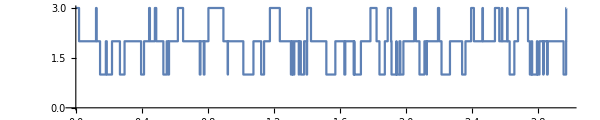

```mathematica
ListStepPlot[straj1,ImageSize->600,AspectRatio->0.2,PlotRange->All]
```

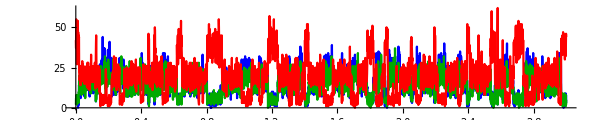

```mathematica
Addt[dat_List]:={binning (Range[Length[dat]]-0.5),dat}ᵀ
{nb,ng,nr}=mcs1ᵀ;
mcspl=ListPlot[Addt/@{nb,ng,nr},Joined->True,PlotStyle->{Blue,Darker@Green,Red},ImageSize->600,AspectRatio->0.2,PlotRange->All]
```

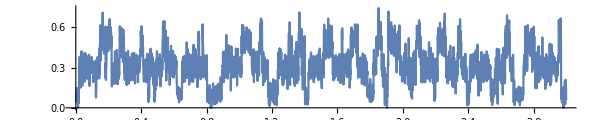

```mathematica
ListPlot[Addt@(nb/(nb+ng+nr)),Joined->True,ImageSize->600,AspectRatio->0.2,PlotRange->All]
```

#### LogLikelihood maximization on binned data

```mathematica
FHMMInitWithBinnedData[{mcs1,mcs2},binning]
```

```mathematica
FHMMSetPhotonRates[{n1,n2}];
FindMaximum[FHMMLogLikelihood[Km[Abs@{k12,k21,k23,k32}]],{{k12,10},{k21,80},{k23,80},{k32,80}},PrecisionGoal->4,AccuracyGoal->4,Method->"IPOPT"]
```

{-53758.,{k12→47.9581,k21→-16.9828,k23→-9.55503,k32→35.2145}}

#### LogLikelihood maximization on photon-by-photon data

```mathematica
FHMMInitWithPhotonByPhotonData[{ptraj1,ptraj2}]
```

```mathematica
FHMMSetPhotonRates[{n1,n2}];
FindMaximum[FHMMLogLikelihood[Km[Abs@{k12,k21,k23,k32}]],{{k12,10},{k21,80},{k23,80},{k32,80}},PrecisionGoal->4,AccuracyGoal->4,Method->"IPOPT"]
```

{4.17396×10^6,{k12→49.0622,k21→-17.5147,k23→9.56155,k32→35.1883}}

#### Viterbi and dwell-time analysis

```mathematica
FHMMInitWithPhotonByPhotonData[{ptraj1,ptraj2}]
dwells=FHMMViterbi[K,{n1,n2}];
```

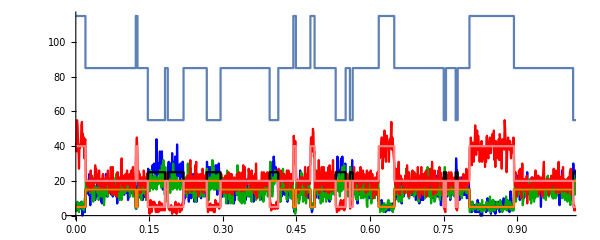

```mathematica
BlueRatefunc[state_]:=n1[[1,state]]*binning
GreenRatefunc[state_]:=n1[[2,state]]*binning
RedRatefunc[state_]:=n1[[3,state]]*binning
viterbimcs=dwells[[1]]["mcs",t0=0,#]&/@{BlueRatefunc,GreenRatefunc,RedRatefunc};
stategraph=dwells[[1]]["stategraph",t0,scale=30,offset=25];

Show[mcspl
,ListPlot[viterbimcs,PlotRange->All,Joined->True,PlotStyle->{Black,Orange,Pink}]
,ListPlot[stategraph,PlotRange->All,Joined->True]
,PlotRange->{{0,1},All},AspectRatio->0.4,ImageSize->600]
```

```mathematica
1/Mean@Flatten@dwells[1->2]["dt"]
1/Mean@Flatten@dwells[2->_]["dt"]
1/Mean@Flatten@dwells[3->2]["dt"]
```

46.0841

25.8661

37.2931

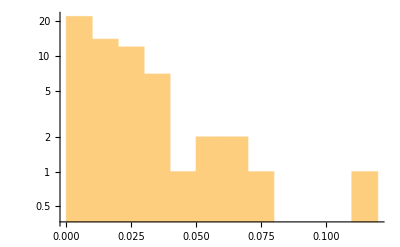

```mathematica
Histogram[Flatten@dwells[1->2]["dt"],Automatic,"LogCount"]
```

```mathematica
dwelltimehisto[trans_]:=Histo[Flatten@dwells[trans]["dt"],{0,0.05,0.01},FOutput->FData][[All,1;;2]]
```

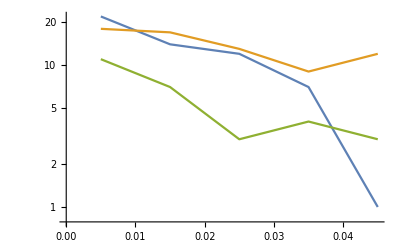

```mathematica
ListLogPlot[{dwelltimehisto[1->2],dwelltimehisto[2->_],dwelltimehisto[3->2]},Joined->True]
```

```mathematica
FHMMInitWithPhotonByPhotonData[{FHMMSimulatePhotonByPhotonTrace[n1,K,60][[1]]}]
```

```mathematica
dwells=FHMMViterbi[K,{n1}];
```

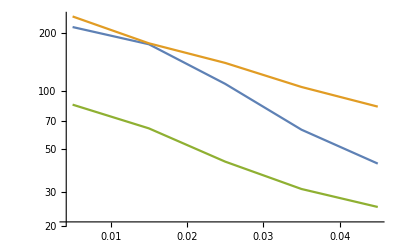

```mathematica
ListLogPlot[{dwelltimehisto[1->2],dwelltimehisto[2->_],dwelltimehisto[3->2]},PlotRange->All,Joined->True]
```

| Related Guides
▪Fretica